```mathematica
Subscript[m, e]=Entity["Particle","Electron"][EntityProperty["Particle","Mass"]];
Subscript[m, α]=Entity["Isotope","Helium4"][EntityProperty["Isotope","AtomicMass"]];
qe=Entity["Particle","Electron"][EntityProperty["Particle","Charge"]];
ρ=Entity["Chemical","Ethanol"][EntityProperty["Chemical","VaporDensity"]];
Subscript[I, Bloch]=14Quantity[10,"eV"];
Subscript[En, 0]=Quantity[5.407,"MeV"];
Subscript[ϵ, 0]=Quantity[, "ElectricConstant"];
z=2;
```

```mathematica
Subscript[v, 0]=v/.Last@Solve[(Subscript[m, α] Quantity[, "SpeedOfLight"]^2)/(√(1-v^2/Quantity[, "SpeedOfLight"]^2))-Subscript[m, α] Quantity[, "SpeedOfLight"]^2==Subscript[En, 0],v]
```

1.6128×10^7 m/s

```mathematica
Subscript[n, air]=Quantity[, "AvogadroConstant"]/Quantity[, "MolarMassConstant"](Entity["Chemical","MolecularNitrogen"][EntityProperty["Chemical","Density"]]*14/28.014+Entity["Element","Oxygen"][EntityProperty["Element","Density"]]*16/31.998);
Subscript[n, CF4]=Quantity[, "AvogadroConstant"]/Quantity[, "MolarMassConstant"]Quantity[3.72,"g/L"]*42/88.0043;
```

```mathematica
Subscript[n, air]/Subscript[n, CF4]
```

0.754622

```mathematica
{Subscript[m, e],Subscript[m, α],qe,ρ,Subscript[I, Bloch],Subscript[v, 0],Subscript[ϵ, 0],Subscript[n, air],Subscript[n, CF4]}=QuantityMagnitude/@UnitConvert/@{Subscript[m, e],Subscript[m, α],qe,ρ,Subscript[I, Bloch],Subscript[v, 0],Subscript[ϵ, 0],Subscript[n, air],Subscript[n, CF4]};
```

```mathematica
eqn=-Dt[v[t],t]==(4π Subscript[n, air] z^2)/(Subscript[m, α] Subscript[m, e] v[t]^2)(qe/(4π Subscript[ϵ, 0]))^2 Log[(2 Subscript[m, e] v[t]^2)/Subscript[I, Bloch]];
```

```mathematica
NDSolve[{eqn,v[0]==Subscript[v, 0]},v[t],{t,0,10^-46},Method->"ExplicitRungeKutta",MaxStepFraction->1/1000]
```

{{v[t]→InterpolatingFunction[…][t]}}

```mathematica
%95⟦1,1,2⟧
```

InterpolatingFunction[…][t]

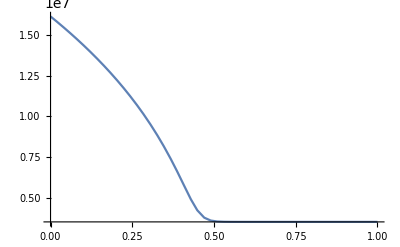

```mathematica
Plot[%96,{t,0.,1.*^-46}]
```

```mathematica
3.24*1.59*10^-3
```

0.0051516

```mathematica
3.24*QuantityMagnitude@Quantity[0.5959, ("Kilograms")/("Meters")^3]*10^-3
```

0.00193072